# Submanifolds

```mathematica
(*Clear stored values*)
ClearAll["Global`*"];
```

```mathematica
(*Define the energy density of dark matter (z) and the energy density of radiation (v) in terms of the energy density of dark energy (x)*)
z[x_,c_]=c*((x-R)/(1-x))^(1/(1-R));

v[x_,cv_]=cv*((x-R)/(1-x))^(4/(3*(1-R)));
```

```mathematica
(*Define the scale factor (a) in terms of x*)
(*ca is the integration constant of a(x)*)
ca[x0_]=(1-x0)/(x0-R);
a[x_,x0_]=(ca[x0]*((x-R)/(1-x)))^((-1)/(3*(1-R)));
```

```mathematica
(*Define the scale factor in terms of compact Z*)
az[Z_,Z0_]=(((1-Z)/Z)(Z0/(1-Z0)))^(1/3);
```

```mathematica
(*Define R and cv*)
R=0.05;
cv=0.000034;
```

```mathematica
(*Import values of c*)
c=Flatten[Import["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\cValues.csv"]]
```

{0.05,0.200851,0.25,0.319517,0.35,0.386125,0.5}

```mathematica
(*Define w, the the RHS of y'*)
w[x_,Y_,z2_,v2_]=-Y^2*(1-Y^2)-(1/6)*(1-Y^2)^(3/2)*(z2+2v2-3*R+x*(1+3*R)-3*x^2);
```

```mathematica
(*Define the Flat Friedmann Separatrix*)
(*Define ffs = Y^2/(1-Y^2)*)
ffs[x_,z2_,v2_]=x/3+z2/3+v2/3;
```

```mathematica
(*Rearrange the above for Y*)
```

```mathematica
FFS[x_,z2_,v2_]=Sqrt[ffs[x,z2,v2]/(1+ffs[x,z2,v2])];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) in terms of a(x)*)
(*Define cfs = Y^2/(1-Y^2)*)
cfs[x_,x0_,z2_,z20_,v2_,v20_]= x/3+z2/3+v2/3-(x0/3+z20/3+v20/3)/(a[x,x0]^2);
```

```mathematica
(*Rearrange above equation for Y*)
CFS[x_,x0_,z2_,z20_,v2_,v20_]=Sqrt[cfs[x,x0,z2,z20,v2,v20]/(1+cfs[x,x0,z2,z20,v2,v20])];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) in terms of a(Z)*)
(*Define cfs = Y^2/(1-Y^2)*)
cfsZ[x_,x0_,Z_,Z0_,v2_,v20_]= x/3+Z/(3*(1-Z))+v2/3-(x0/3+Z0/(3*(1-Z0))+v20/3)/(az[Z,Z0]^2);
```

```mathematica
(*Rearrange above equation for Y*)
CFSZ[x_,x0_,Z_,Z0_,v2_,v20_]=Sqrt[cfsZ[x,x0,Z,Z0,v2,v20]/(1+cfsZ[x,x0,Z,Z0,v2,v20])];
```

```mathematica
(*Set up plot for x = R and x = 1 seperatrices*)
Sepx=ContourPlot[{x==R,x==1},{x,0,1.1},{Y,-1,1},ContourStyle->{Black},PlotRange->Full];
```

## z = 0 Submanifold

### Find the Y = 0 fixed points

```mathematica
zY0=FindRoot[w[x,0,0,v[x,cv]]==0,{x,0}];
```

```mathematica
zY0=x/.zY0
```

0.191678-0.115164 ⅈ

### Plot the Phase Space

```mathematica
(*Trajectories for the phase space*)
trajz[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
ztraj[1]=ContourPlot[Evaluate[trajz[0,0.1]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[2]=ContourPlot[Evaluate[trajz[0,0.3]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[3]=ContourPlot[Evaluate[trajz[0,0.5]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[4]=ContourPlot[Evaluate[trajz[0,0.7]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[5]=ContourPlot[Evaluate[trajz[0,0.9]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[6]=ContourPlot[Evaluate[trajz[0.4,0.4]],{x,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[7]=ContourPlot[Evaluate[trajz[0.4,0.4]],{x,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[8]=ContourPlot[Evaluate[trajz[0.9,0.3]],{x,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ztraj[9]=ContourPlot[Evaluate[trajz[0.9,0.3]],{x,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajz=Table[ztraj[i],{i,1,9}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSz=Plot[{FFS[x,0,v[x,cv]],-FFS[x,0,v[x,cv]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
(*CFSz=Plot[{{CFS[x,zY0,0,0,v[x,cv],v[zY0,cv]]},{-CFS[x,zY0,0,0,v[x,cv],v[zY0,cv]]}},{x,0,1},PlotStyle->Black];*)
```

```mathematica
(*Plot the fixed points*)
FPShowz = ListPlot[{{1,1},{1,-1}, {R,Sqrt[R/(3+R)]},{R,-Sqrt[R/(3+R)]},{zY0,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

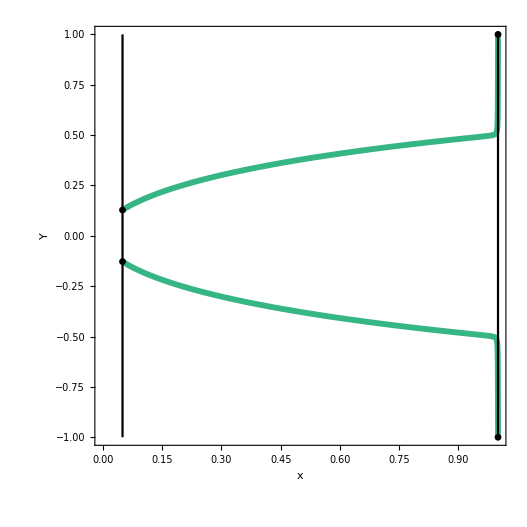

```mathematica
zSubMan=Show[Trajz,FFSz,FPShowz,Sepx,FrameLabel->{"x","Y"}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\zSubMan.pdf",zSubMan]*)
```

## x = R Submanifold

### Y = 0 fixed points

```mathematica
xRY0=2*R/(1+2*R);
```

### Plot the Phase Space

```mathematica
(*Trajectories for the phase space*)
trajxR[Y0_,Z0_]:=Y^2/(1-Y^2)==R/3+Z/(3*(1-Z))+v[R,cv]/3-(1/az[Z,Z0]^2)*(R/3+Z0/(3*(1-Z0))+v[R,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
xRtraj[1]=ContourPlot[Evaluate[trajxR[0,0.03]],{Z,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[2]=ContourPlot[Evaluate[trajxR[0,0.03]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[3]=ContourPlot[Evaluate[trajxR[0,0.6]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[4]=ContourPlot[Evaluate[trajxR[0,0.9]],{Z,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[5]=ContourPlot[Evaluate[trajxR[0.4,0.45]],{Z,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[6]=ContourPlot[Evaluate[trajxR[0.4,0.45]],{Z,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[7]=ContourPlot[Evaluate[trajxR[0.9,0.3]],{Z,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[8]=ContourPlot[Evaluate[trajxR[0.9,0.3]],{Z,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[9]=ContourPlot[Evaluate[trajxR[0.75,0.5]],{Z,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xRtraj[10]=ContourPlot[Evaluate[trajxR[0.75,0.5]],{Z,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajxR=Table[xRtraj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSxR=Plot[{FFS[R,Z/(1-Z),v[R,cv]],-FFS[R,Z/(1-Z),v[R,cv]]},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSxR=Plot[{{CFSZ[R,R,Z,xRY0,v[R,cv],v[R,cv]]},{-CFSZ[R,R,Z,xRY0,v[R,cv],v[R,cv]]}},{Z,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowxR=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,Sqrt[R/(3+R)]},{0,-Sqrt[R/(3+R)]},{xRY0,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

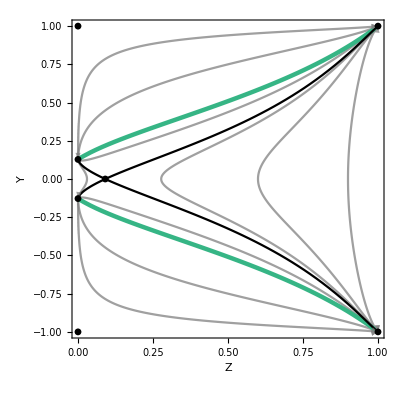

```mathematica
xRSubMan=Show[TrajxR,FFSxR,CFSxR,FPShowxR,FrameLabel->{"Z",Rotate["Y",300]},PlotRange->{{0,1},{-1,1}}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\xRSubMan.pdf",xRSubMan]*)
```

## x = 1 Submanifold

### Find the Y = 0 fixed points

```mathematica
Clear[zY0FixedPoints]
```

```mathematica
zY0=FindRoot[w[x,0,0,v[x,cv]]==0,{x,0}];
```

```mathematica
zY0=x/.zY0
```

0.191678-0.115164 ⅈ

```mathematica
zY0FixedPoints=ListPlot[{{zY0,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

### Plot the Phase Space

```mathematica
(*Trajectories for the phase space*)
trajz[Y0_,Z0_]:=Y^2/(1-Y^2)==1/3+Z/(3*(1-Z))+v[1,cv]/3-(1/az[Z,Z0]^2)*(1/3+Z0/(3*(1-Z0))+v[1,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
ztraj[1]=ContourPlot[Evaluate[trajz[0,0.1]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1/3+Z/(3 (1-Z))+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
ztraj[2]=ContourPlot[Evaluate[trajz[0,0.3]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1/3+Z/(3 (1-Z))+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
ztraj[3]=ContourPlot[Evaluate[trajz[0,0.5]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1/3+Z/(3 (1-Z))+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
ztraj[4]=ContourPlot[Evaluate[trajz[0,0.7]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1/3+Z/(3 (1-Z))+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
ztraj[5]=ContourPlot[Evaluate[trajz[0,0.9]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1/3+Z/(3 (1-Z))+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
ztraj[6]=ContourPlot[Evaluate[trajz[0.4,0.4]],{x,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1/3+Z/(3 (1-Z))+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
ztraj[7]=ContourPlot[Evaluate[trajz[0.4,0.4]],{x,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1/3+Z/(3 (1-Z))+ComplexInfinity+ComplexInfinity encountered.

```mathematica
ztraj[8]=ContourPlot[Evaluate[trajz[0.9,0.3]],{x,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1/3+Z/(3 (1-Z))+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
ztraj[9]=ContourPlot[Evaluate[trajz[0.9,0.3]],{x,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 1/3+Z/(3 (1-Z))+ComplexInfinity+ComplexInfinity encountered.

```mathematica
(*Add trajectories into a table*)
Trajz=Table[ztraj[i],{i,1,9}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSz=Plot[{FFS[x,0,v[x,cv]],-FFS[x,0,v[x,cv]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
(*CFSz=Plot[{{CFS[x,zY0,0,0,v[x,cv],v[zY0,cv]]},{-CFS[x,zY0,0,0,v[x,cv],v[zY0,cv]]}},{x,0,1},PlotStyle->Black];*)
```

Show::gcomb: Could not combine the graphics objects in ….

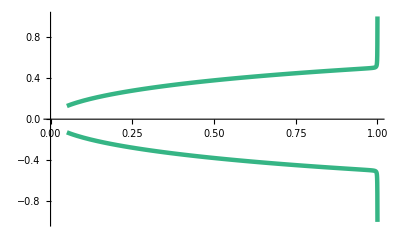
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-,Sep,FPShow,-Graphics-]

```mathematica
zSubMan=Show[Trajz,FFSz,Sep,FPShow,zY0FixedPoints]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\zSubMan.pdf",zSubMan]*)
```

## Y = 0 Submanifold

### Plot the Phase Space

```mathematica
(*Trajectories for the phase space*)
trajY[const_]:=const
```

```mathematica
Ytraj[1]=Plot[Evaluate[trajY[0]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[2]=Plot[Evaluate[trajY[0.2]],{x,0,0.5},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[3]=Plot[Evaluate[trajY[0.4]],{x,0,0.65},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[4]=Plot[Evaluate[trajY[0.6]],{x,0,0.9},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[5]=Plot[Evaluate[trajY[0.8]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[6]=Plot[Evaluate[trajY[1]],{x,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[7]=Plot[Evaluate[trajY[0.2]],{x,0.5,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[8]=Plot[Evaluate[trajY[0.4]],{x,0.65,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
Ytraj[9]=Plot[Evaluate[trajY[0.6]],{x,0.9,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}},Frame->True,PlotRange->{{0,1},{-0.05,1.05}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
TrajY=Table[Ytraj[i],{i,1,9}];
```

```mathematica
(*Curve of possible Einstein points (where Y = 0)*)
SepY=ContourPlot[{Z/(1-Z)==3*R-(1+3*R)*x+3*x^2-2*v[x,cv]},{x,0,1},{Z,0,1},ContourStyle->{Black},Frame->True,PlotRange->{{0,1},{-0.05,1.05}},PlotPoints->200];
```

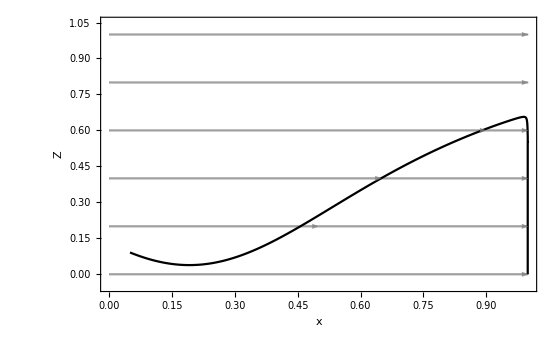

```mathematica
(*Show all components of plot*)
YSubMan=Show[TrajY,SepY,FrameLabel->{"x","Z"}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\YSubMan.pdf",YSubMan]*)
```

## k = 0 Submanifold

### Plot the Phase Space

```mathematica
(*Defining c, the first integral of z(x), for this case*)
z0[Y0_,x0_]=3*Y0^2/(1-Y0^2)-x0-v[x0,cv];
cz[Y0_,x0_]=z0[Y0,x0]*((1-x0)/(x0-R))^(1/(1-R));
```

```mathematica
(*Trajectories for the phase space*)
trajk[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,cz[Y0,x0]]/3+v[x,cv]/3;
```

```mathematica
ktraj[1]=ContourPlot[Evaluate[trajk[0,0.2]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[2]=ContourPlot[Evaluate[trajk[0,0.03]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[3]=ContourPlot[Evaluate[trajk[0,0.6]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[4]=ContourPlot[Evaluate[trajk[0,0.9]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[5]=ContourPlot[Evaluate[trajk[0.4,0.45]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[6]=ContourPlot[Evaluate[trajk[0.4,0.45]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[7]=ContourPlot[Evaluate[trajk[0.9,0.3]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[8]=ContourPlot[Evaluate[trajk[0.9,0.3]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[9]=ContourPlot[Evaluate[trajk[0.75,0.5]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
ktraj[10]=ContourPlot[Evaluate[trajk[0.75,0.5]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajk=Table[ktraj[i],{i,1,10}];
```

```mathematica
(*Seperatrix where z = 0*)
Sepk=ContourPlot[{3*Y^2/(1-Y^2)-x-v[x,cv]==0},{x,0,1},{Y,-1,1},ContourStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]},PlotPoints->100];
```

```mathematica
(*Fixed points of the system*)
FPShowk=ListPlot[{{1,1/2},{1,-1/2},{1,1},{1,-1},{R,1},{R,-1},{R,Sqrt[R/(3+R)]},{R,-Sqrt[R/(3+R)]}},PlotStyle->{Black},PlotMarkers->{Automatic,Medium}, PlotStyle->{Black}];
```

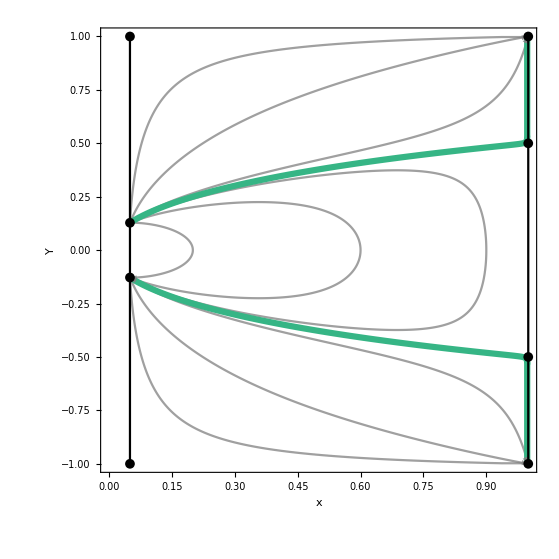

```mathematica
(*Show all components of plot*)
YSubMan=Show[Trajk,Sepk,FPShowk,Sepx,FrameLabel->{"x",Rotate["Y",300]}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\Submanifolds\\YSubMan.pdf",YSubMan]*)
```